```mathematica
(*why doesn't the ensemble sum over different combinations of Subscript[Q, 1] and Subscript[Q, 2] aswell?*)
(*Replace Q and g constants by Q^2 and g^2?*)
(*idea for analytical manipulation: do τ integral first?*)

GeVtofm=0.1973; (*1 GeV = GeVtofm / 1 fm -- should use more algarisms?*)
Subscript[v, perp]=1.0; (*adimensional*)
Subscript[v, paral]=0; (*adimensional*)
v=√(Subscript[v, perp]^2+Subscript[v, paral]^2); (*adimensional - should v always equal 1?*)
Subscript[N, c]=3;
g=1.0; (*adimensional*)
T=1.0; 
Subscript[Q, 1]=2.0;  (*GeV*)
Subscript[Q, 2]=2.0;(*GeV*)

r2[τ_,τʹ_,φ_,ϕ_]:=(Subscript[v, perp]*(τ-τʹ)+(τʹ*Cos[φ]-τ*Cos[ϕ]))^2+(τʹ*Sin[φ]-τ*Sin[ϕ])^2(*GeV^-2*) (*0 ⩽ r^(2□) ⩽(τ-τʹ)^2((1+Subscript[v, perp])^2+1)*)
GGBW[x_,Q_]:=Q^2/(g^2*Subscript[N, c])*(1-Exp[-x])/x(*GeV^2*) 
GBWArg[r2_,Q_]:=(Q^2*r2)/4(*adimensional*)

(*STOPPING POWER*)
IntegrandStoppingPower[τ_,τʹ_,φ_,ϕ_]:=GGBW[GBWArg[r2[τ,τʹ,φ,ϕ],Subscript[Q, 1]],Subscript[Q, 1]]*GGBW[GBWArg[r2[τ,τʹ,φ,ϕ],Subscript[Q, 2]],Subscript[Q, 2]]*(Subscript[v, paral]^2+Subscript[v, perp]^2*Sin[φ]*Sin[ϕ])(*GeV^4*)
stoppingPower[τ_]:=-1/(v*T)*g^4/4*(Subscript[N, c]^2-1)*NIntegrate[IntegrandStoppingPower[τ,τʹ,φ,ϕ],{φ,0,2π},{ϕ,0,2π},{τʹ,0,τ}] (*GeV^2*)

(*QHAT*)
IntegrandQhat[τ_,τʹ_,φ_,ϕ_]:=GGBW[GBWArg[r2[τ,τʹ,φ,ϕ],Subscript[Q, 1]],Subscript[Q, 1]]*GGBW[GBWArg[r2[τ,τʹ,φ,ϕ],Subscript[Q, 2]],Subscript[Q, 2]]*(Subscript[v, paral]^2*Cos[ϕ-φ]+Subscript[v, perp]^2*(Cos[φ]*Cos[ϕ]+1))(*GeV^4*)
Qhat[τ_]:=g^4/4*(Subscript[N, c]^2-1)*(1+v^2)/v^3*NIntegrate[IntegrandQhat[τ,τʹ,φ,ϕ],{φ,0,2π},{ϕ,0,2π},{τʹ,0,τ}] (*GeV^3*)
```

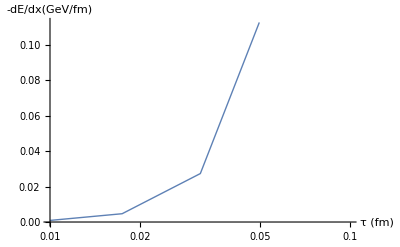

```mathematica
LogLinearPlot[-stoppingPower[τ/GeVtofm]*GeVtofm,{τ,0.01,0.1},PlotPoints->5,MaxRecursion->0,AxesLabel->{"τ (fm)","-dE/dx(GeV/fm)"},PlotStyle->Thick](*GeV/fm as function of fm*)
```

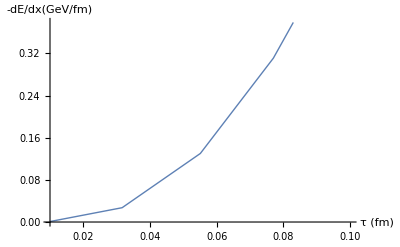

```mathematica
Plot[-stoppingPower[τ/GeVtofm]*GeVtofm,{τ,0.01,0.1},PlotPoints->5,MaxRecursion->0,AxesLabel->{"τ (fm)","-dE/dx(GeV/fm)"},PlotStyle->Thick]
```

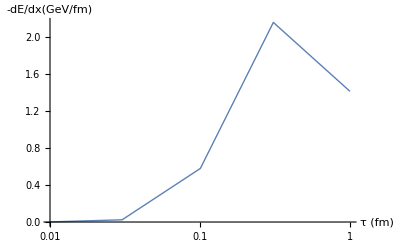

```mathematica
LogLinearPlot[-stoppingPower[τ/GeVtofm]*GeVtofm,{τ,0.01,1},PlotPoints->5,MaxRecursion->0,AxesLabel->{"τ (fm)","-dE/dx(GeV/fm)"},PlotStyle->Thick]
```

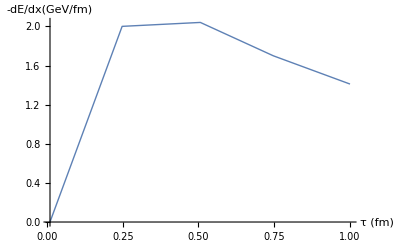

```mathematica
Plot[-stoppingPower[τ/GeVtofm]*GeVtofm,{τ,0.01,1},PlotPoints->5,MaxRecursion->0,AxesLabel->{"τ (fm)","-dE/dx(GeV/fm)"},PlotStyle->Thick]
```

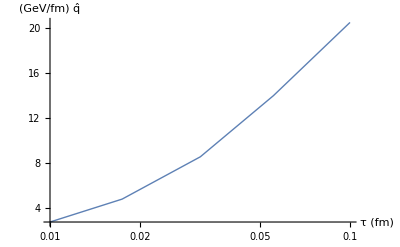

```mathematica
LogLinearPlot[Qhat[τ/GeVtofm]*GeVtofm,{τ,0.01,0.1},PlotPoints->5,MaxRecursion->0,AxesLabel->{"τ (fm)",OverHat[q]"(GeV^2/fm)"},PlotStyle->Thick] (*GeV^2/fm as function of fm*)
```

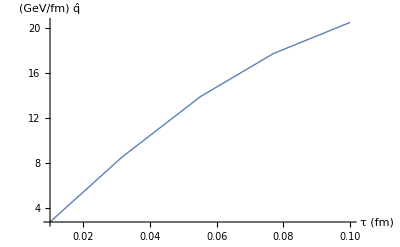

```mathematica
Plot[Qhat[τ/GeVtofm]*GeVtofm,{τ,0.01,0.1},PlotPoints->5,MaxRecursion->0,AxesLabel->{"τ (fm)",OverHat[q]"(GeV^2/fm)"},PlotStyle->Thick]
```

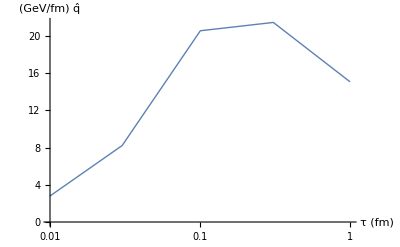

```mathematica
LogLinearPlot[Qhat[τ/GeVtofm]*GeVtofm,{τ,0.01,1},PlotPoints->5,MaxRecursion->0,AxesLabel->{"τ (fm)",OverHat[q]"(GeV^2/fm)"},PlotStyle->Thick]
```

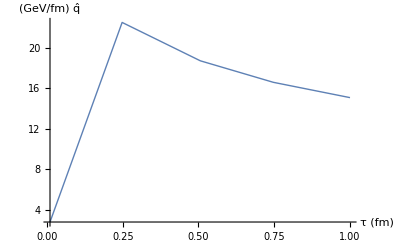

```mathematica
Plot[Qhat[τ/GeVtofm]*GeVtofm,{τ,0.01,1},PlotPoints->5,MaxRecursion->0,AxesLabel->{"τ (fm)",OverHat[q]"(GeV^2/fm)"},PlotStyle->Thick]
```